#### Importing data from Julia

```mathematica
SetDirectory[NotebookDirectory[]];
datawf=Import["output/wavefunction.dat"];
datawigner=Import["output/wignerfunction.dat"];
```

```mathematica
NN=300;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
L=2*10;(* Size of the space (must coincide the N in the Julia code)*)
Wvol=Sum[(L/NN)*(L/NN)*datawigner[[i,3]],{i,1,Length[datawigner]}](*Volume of the Wigner function*)
Wneg=Sum[(L/NN)*(L/NN)*Abs[datawigner[[i,3]]],{i,1,Length[datawigner]}]-Wvol(*Wigner negativity*)
```

0.989082

0.632129

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

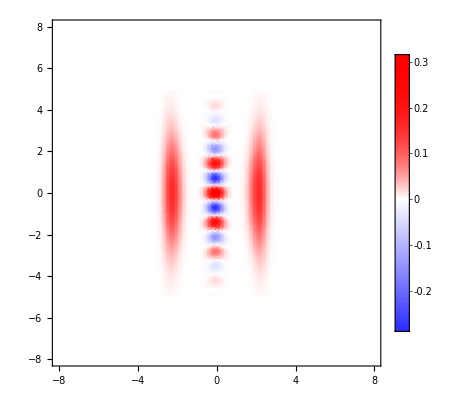

```mathematica
(*Wigner function and Poncaire sections*)wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-8,8},{-8,8},All},Frame->  True,LabelStyle->Directive[Bold,Medium],ColorFunction->(FCo[1-0.5/0.35 (#+0.35)]&),ColorFunctionScaling->False,PlotLegends->Automatic],ListPlot[{},PlotStyle->Darker[Green]]]
```

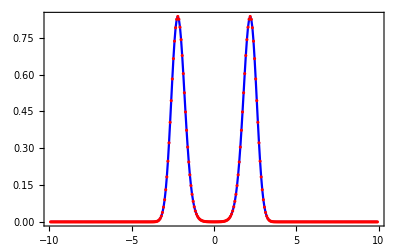

```mathematica
(*Probability density*)
datawfn=Table[{datawf[[i,1]],Abs[datawf[[i,2]]+I*datawf[[i,3]]]},{i,1,Length[datawf]}];
ListPlot[{datawfn,datawfn},PlotRange->{All,All},Joined->{True,False},Frame->True,LabelStyle->{Black,15},PlotStyle->{Blue,Red}]
```